```mathematica
n=3;
y[x_,κ_]=√(1/κ^2-x^2)-1/κ;
X[κ_]={#,y[#,κ]}&/@Range[-1,1,2/(n-1)];
Manipulate[Plot[√(1/κ^2-x^2)-1/κ,{x,-1,1},PlotRange->{{-1,1},{-1,1}},AspectRatio->1],{{κ,1},0,1}]
Manipulate[ListPlot[X[κ],PlotRange->{{-1,1},{-1,0.5}},AspectRatio->3/4],{{κ,1},0.0001,1}]
Assuming[κ>0,Series[y[x,κ],{κ,0,10}]]
```

-(x^2 κ)/2-(x^4 κ^3)/8-(x^6 κ^5)/16-(5 x^8 κ^7)/128-(7 x^10 κ^9)/256+O[κ]^11

```mathematica
F=Table[i,{i,1,n}];
ϕ[xi_,ϵ_]=ⅇ^(-(ϵ xi)^2);
(A[ϵ_,κ_]=Assuming[κ>0,Table[ϕ[Norm[X[κ][[i]]-X[κ][[j]]],ϵ],{i,1,n},{j,1,n}]]//FullSimplify)//MatrixForm
Assuming[κ>0,Asymptotic[LinearSolve[A[ϵ,κ],F],{κ,0,2}]]//MatrixForm
Assuming[κ>0,Asymptotic[Eigenvalues[A[ϵ,κ]],{κ,0,4}]]//MatrixForm
Eigenvalues[lim_(κ->0) A[ϵ,κ]]//MatrixForm
```

(1 | ⅇ^(-ϵ^2 (1+Abs[√(-1+1/κ^2)-√(1/κ^2)]^2)) | ⅇ^(-4 ϵ^2)
ⅇ^(-ϵ^2 (1+Abs[√(-1+1/κ^2)-√(1/κ^2)]^2)) | 1 | ⅇ^(-ϵ^2 (1+Abs[√(-1+1/κ^2)-√(1/κ^2)]^2))
ⅇ^(-4 ϵ^2) | ⅇ^(-ϵ^2 (1+Abs[√(-1+1/κ^2)-√(1/κ^2)]^2)) | 1)

((ⅇ^(3 ϵ^2) (-1+ⅇ^(ϵ^2))^2 (2+ⅇ^(ϵ^2)+ⅇ^(3 ϵ^2)))/((-1+ⅇ^(2 ϵ^2))^2 (-1+ⅇ^(4 ϵ^2)))+(ⅇ^(3 ϵ^2) (-1-ⅇ^(ϵ^2)-3 ⅇ^(2 ϵ^2)+ⅇ^(3 ϵ^2)) ϵ^2 κ^2)/(2 (-1+ⅇ^(ϵ^2))^3 (1+ⅇ^(ϵ^2))^4)
(2 ⅇ^(-ϵ^2) (ⅇ^(ϵ^2)-2 ⅇ^(4 ϵ^2)+ⅇ^(5 ϵ^2)))/((-1+ⅇ^(2 ϵ^2))^2)+(ⅇ^(2 ϵ^2) (2+ⅇ^(ϵ^2)+ⅇ^(2 ϵ^2)-ⅇ^(3 ϵ^2)+ⅇ^(4 ϵ^2)) ϵ^2 κ^2)/((-1+ⅇ^(ϵ^2))^3 (1+ⅇ^(ϵ^2))^4)
(ⅇ^(3 ϵ^2) (2+ⅇ^(ϵ^2)+3 ⅇ^(2 ϵ^2)))/((-1+ⅇ^(ϵ^2)) (1+ⅇ^(ϵ^2))^2 (1+ⅇ^(2 ϵ^2)))+(ⅇ^(3 ϵ^2) (-1-ⅇ^(ϵ^2)-3 ⅇ^(2 ϵ^2)+ⅇ^(3 ϵ^2)) ϵ^2 κ^2)/(2 (-1+ⅇ^(ϵ^2))^3 (1+ⅇ^(ϵ^2))^4))

(ⅇ^(-4 ϵ^2) (-1+ⅇ^(4 ϵ^2))
1/2 ⅇ^(-5 ϵ^2) (ⅇ^(ϵ^2)+2 ⅇ^(5 ϵ^2)-√(ⅇ^(2 ϵ^2) (1+8 ⅇ^(6 ϵ^2))))+(ⅇ^(ϵ^2) √(ⅇ^(2 ϵ^2) (1+8 ⅇ^(6 ϵ^2))) ϵ^2 κ^2)/(1+8 ⅇ^(6 ϵ^2))-(ⅇ^(ϵ^2) √(ⅇ^(2 ϵ^2) (1+8 ⅇ^(6 ϵ^2))) ϵ^2 (-2-16 ⅇ^(6 ϵ^2)+ϵ^2+4 ⅇ^(6 ϵ^2) ϵ^2) κ^4)/(4 (1+8 ⅇ^(6 ϵ^2))^2)
1/2 ⅇ^(-5 ϵ^2) (ⅇ^(ϵ^2)+2 ⅇ^(5 ϵ^2)+√(ⅇ^(2 ϵ^2) (1+8 ⅇ^(6 ϵ^2))))-(ⅇ^(ϵ^2) √(ⅇ^(2 ϵ^2) (1+8 ⅇ^(6 ϵ^2))) ϵ^2 κ^2)/(1+8 ⅇ^(6 ϵ^2))+(ⅇ^(ϵ^2) √(ⅇ^(2 ϵ^2) (1+8 ⅇ^(6 ϵ^2))) ϵ^2 (-2-16 ⅇ^(6 ϵ^2)+ϵ^2+4 ⅇ^(6 ϵ^2) ϵ^2) κ^4)/(4 (1+8 ⅇ^(6 ϵ^2))^2))

(ⅇ^(-4 ϵ^2) (-1+ⅇ^(4 ϵ^2))
1/2 ⅇ^(-4 ϵ^2) (1+2 ⅇ^(4 ϵ^2)-√(1+8 ⅇ^(6 ϵ^2)))
1/2 ⅇ^(-4 ϵ^2) (1+2 ⅇ^(4 ϵ^2)+√(1+8 ⅇ^(6 ϵ^2))))

```mathematica
(A[ϵ_,κ_]=Assuming[κ>0,Table[ϕ[Norm[X[κ][[i]]-X[κ][[j]]],ϵ],{i,1,n},{j,1,n}]]//FullSimplify)//MatrixForm
Assuming[κ>0,Asymptotic[A[ϵ,κ],{κ,0,4}]]//MatrixForm
```

(1 | ⅇ^(-ϵ^2 (1+Abs[√(-1+1/κ^2)-√(1/κ^2)]^2)) | ⅇ^(-4 ϵ^2)
ⅇ^(-ϵ^2 (1+Abs[√(-1+1/κ^2)-√(1/κ^2)]^2)) | 1 | ⅇ^(-ϵ^2 (1+Abs[√(-1+1/κ^2)-√(1/κ^2)]^2))
ⅇ^(-4 ϵ^2) | ⅇ^(-ϵ^2 (1+Abs[√(-1+1/κ^2)-√(1/κ^2)]^2)) | 1)

(1 | ⅇ^(-ϵ^2)-1/4 ⅇ^(-ϵ^2) ϵ^2 κ^2+1/32 ⅇ^(-ϵ^2) ϵ^2 (-4+ϵ^2) κ^4 | ⅇ^(-4 ϵ^2)
ⅇ^(-ϵ^2)-1/4 ⅇ^(-ϵ^2) ϵ^2 κ^2+1/32 ⅇ^(-ϵ^2) ϵ^2 (-4+ϵ^2) κ^4 | 1 | ⅇ^(-ϵ^2)-1/4 ⅇ^(-ϵ^2) ϵ^2 κ^2+1/32 ⅇ^(-ϵ^2) ϵ^2 (-4+ϵ^2) κ^4
ⅇ^(-4 ϵ^2) | ⅇ^(-ϵ^2)-1/4 ⅇ^(-ϵ^2) ϵ^2 κ^2+1/32 ⅇ^(-ϵ^2) ϵ^2 (-4+ϵ^2) κ^4 | 1)

```mathematica
Assuming[κ>0,ⅇ^(-ϵ^2(√(1/κ^2-ri^2)-√(1/κ^2-rj^2))^2)+O[κ]^6]
```

1-1/4 ((-ri^2+rj^2)^2 ϵ^2) κ^2+1/4 (-1/2 (-ri^2+rj^2) (-ri^4+rj^4) ϵ^2+1/8 (-ri^2+rj^2)^4 ϵ^4) κ^4+O[κ]^6

ⅇ^(-(((xi-xj)^2+(yi-yj)^2) ϵ^2))-1/4 (ⅇ^(-(((xi-xj)^2+(yi-yj)^2) ϵ^2)) (-ri^2+rj^2)^2 ϵ^2) κ^2+1/4 ⅇ^(-(((xi-xj)^2+(yi-yj)^2) ϵ^2)) (-1/2 (-ri^2+rj^2) (-ri^4+rj^4) ϵ^2+1/8 (-ri^2+rj^2)^4 ϵ^4) κ^4+O[κ]^6

1-1/4 ((-ri^2+rj^2)^2 ϵ^2) κ^2+1/4 (-1/2 (-ri^2+rj^2) (-ri^4+rj^4) ϵ^2+1/8 (-ri^2+rj^2)^4 ϵ^4) κ^4+O[κ]^6

```mathematica
ⅇ^(ϵ0+κ^2 ϵ1+O[κ]^4)+O[κ]^4
```

ⅇ^ϵ0+ⅇ^ϵ0 ϵ1 κ^2+O[κ]^4

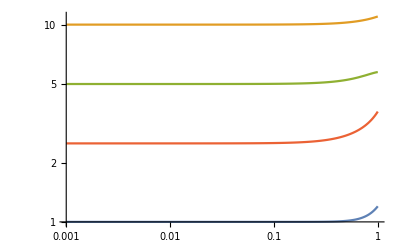

```mathematica
LogLogPlot[{1+0.2 x^4,10+x^2,5+x^2-0.25 x^6,2.5+x^2-0.125 x^4+0.25 x^6},{x,10^-3,1},PlotRange->All]
```

```mathematica
AsymptoticSolve[1/2 ⅇ^(-5 ϵ^2) (ⅇ^(ϵ^2)+2 ⅇ^(5 ϵ^2)-√(ⅇ^(2 ϵ^2) (1+8 ⅇ^(6 ϵ^2))))+(ⅇ^(ϵ^2) √(ⅇ^(2 ϵ^2) (1+8 ⅇ^(6 ϵ^2))) ϵ^2 κ^2)/(1+8 ⅇ^(6 ϵ^2))-(ⅇ^(ϵ^2) √(ⅇ^(2 ϵ^2) (1+8 ⅇ^(6 ϵ^2))) ϵ^2 (-2-16 ⅇ^(6 ϵ^2)+ϵ^2+4 ⅇ^(6 ϵ^2) ϵ^2) κ^4)/(4 (1+8 ⅇ^(6 ϵ^2))^2)==0,{ϵ,0},{κ,0,3}]
```

{{ϵ→0},{ϵ→0},{ϵ→-(ⅈ κ)/2-(ⅈ κ^3)/8},{ϵ→(ⅈ κ)/2+(ⅈ κ^3)/8}}

```mathematica
tmp[κ_]=(ⅈ κ)/2+(ⅈ κ^3)/8;
tmp[0]//N
```

0.